# ECE4010J Final Cheating Sheet

## Linear Regression

## Simple Linear Regression

### Data Import and Visualization in Matrix Form

Data might be defined in this way, in the form of {y, x, y, x,...}

```mathematica
Data:={4.88,0,4.95,0,6.92,4.7,7.00,4.7,8.99,9.5,9.10,9.5,11.09,14.3,11.20,14.3,13.18,19.1,13.30,19.1,15.26,23.9,15.41,24.0,17.39,28.7,17.51,28.7}
X=Take[Data,{2,-1,2}];
Y=Take[Data,{1,-1,2}];
Data=Transpose[{X,Y}];
Print["Visualization of data: ",MatrixForm[Data]](*Please include this step to guarantee the data is in the correct form before performing other steps!*)
```

Visualization of data: (0 | 4.88
0 | 4.95
4.7 | 6.92
4.7 | 7.
9.5 | 8.99
9.5 | 9.1
14.3 | 11.09
14.3 | 11.2
19.1 | 13.18
19.1 | 13.3
23.9 | 15.26
24. | 15.41
28.7 | 17.39
28.7 | 17.51)

### Build Linear Model

```mathematica
n=Length[X];
X2 =(X)^2;
Y2 = (Y)^2;
XY = X.Y;
Sxx=Total[X2]-n*(Mean[X]^2);
Syy=Total[Y2]-n*(Mean[Y]^2);
Sxy =Total[XY] -n*Mean[X]*Mean[Y];
b1 = Sxy/Sxx ;
b0 = Mean[Y]-b1*Mean[X];
SSE = Syy-b1*Sxy;
R2 = Sxy^2 /(Sxx*Syy);
S =Sqrt[ SSE/(n-2)];
Print["n:",n]
Print["X:",Total[X]]
Print["Y:",Total[Y]]
Print["X2:",Total[X2]]
Print["Y2:",Total[Y2]]
Print["XY:",Total[XY]]
Print["SXY:",Sxy]
Print["SXX:",Sxx]
Print["SYY(SST):",Syy]
Print["Y=",b1,"X+",b0]
Print["SSE:",SSE]
Print["Estimated variance: ",S^2]
Print["S：",S]
Print["R2:",R2]
```

n:7

X:28

Y:228

X2:140

Y2:8934

XY:1111

SXY:199

SXX:28

SYY(SST):10554/7

Y=199/28 X+29/7

SSE:2615/28

Estimated variance: 523/28

S：(√(523/7))/2

R2:39601/42216

### Basic Model Analysis

```mathematica
model=LinearModelFit[Data,x,x];
Print["Fitted model: ",model["BestFit"]]
S2=model["EstimatedVariance"];
Print["Estimated variance: ",S2]
R2=model["RSquared"];
R=Sqrt[R2];
Print["R2: ", R2]
```

Fitted model: 4.90738+0.436293 x

Estimated variance: 0.00332122

R2: 0.999837

### Residual Analysis

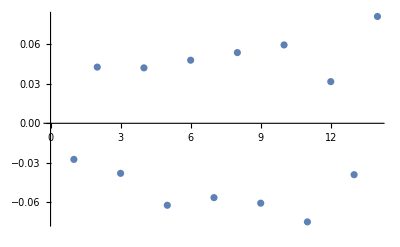

```mathematica
residual=model["FitResiduals"];
ListPlot[residual]
```

### Parameter Table and Parameter Confidence Intervals

```mathematica
model["ParameterTable"]
model["ParameterConfidenceIntervalTable",ConfidenceLevel->0.95]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 4.90738 | 0.0276904 | 177.223 | 7.00201×10^-22
x | 0.436293 | 0.00160678 | 271.532 | 4.18943×10^-24

| Estimate | Standard Error | Confidence Interval
1 | 4.90738 | 0.0276904 | {4.84705,4.96771}
x | 0.436293 | 0.00160678 | {0.432792,0.439794}

### Test for Significance: Student T Distribution

```mathematica
T=b1*Sqrt[Sxx]/S;
P=Probability[t>=Abs[T],t\[Distributed]StudentTDistribution[n-2]];
Print["P-value: ", 2*P ](*Should multiplied by 2.*)
```

P-value: 4.18943×10^-24

```mathematica
T=R*Sqrt[n-2]/Sqrt[1-R^2];
P=Probability[t>=Abs[T],t\[Distributed]StudentTDistribution[n-2]];
Print["P-value: ", 2*P](*Should multiplied by 2.*)
```

P-value: 4.18943×10^-24

### Test for Significance : F Distribution

```mathematica
F=(n-2)*(Syy-SSE)/SSE;
```

```mathematica
P=Probability[f>=F,f\[Distributed]FRatioDistribution[1,n-2]];
Print["P-value: ", P](*There is no need to multiplied by 2.*)
```

P-value: 4.18943×10^-24

### Confidence Interval and Prediction Interval for a Single Point

```mathematica
alpha=0.05;
conf=model["MeanPredictionBands",ConfidenceLevel->1-alpha]/.x->15 ;
pred= model["SinglePredictionBands",ConfidenceLevel->1-alpha]/.x->15 ;
Print["Confidence Band: ",conf, "for ",100(1-alpha),"% confidence level."]
Print["Prediction Band: ",pred, "for ",100(1-alpha),"% confidence level."]
```

Confidence Band: {11.4181,11.4854}for 95.% confidence level.

Prediction Band: {11.3218,11.5818}for 95.% confidence level.

### Lack-of-Fit Problem

```mathematica
SSEpe=Sum[(Y[[i]]-Sum[Y[[j]],{j,1,5}]/5)^2,{i,1,5}]+Sum[(Y[[i]]-Sum[Y[[j]],{j,6,10}]/5)^2,{i,6,10}];
SSElf=SSE-SSEpe;
n=Length[X];
k=8;
F=(SSElf/(k-2))/(SSEpe/(n-k));
P=Probability[f>=F,f\[Distributed]FRatioDistribution[k-2,n-k]];
Print["P-value: ",P]
```

P-value: 0.947082

## Multiple Linear Regression

### Build Model for Polynomial Model: Using Non-linear Model Fit

```mathematica
X:={5,5,10,10,15,15,20,20,25,25};
Y:={14.0,12.5,7.0,5.0,2.1,1.8,6.2,4.9,13.2,14.6};
Data=Transpose[{X,Y}];
Print["Visualization of data: ",MatrixForm[Data]]
```

Visualization of data: (5 | 14.
5 | 12.5
10 | 7.
10 | 5.
15 | 2.1
15 | 1.8
20 | 6.2
20 | 4.9
25 | 13.2
25 | 14.6)

```mathematica
Clear[x];Clear[b0];Clear[b1];Clear[b2];
model=NonlinearModelFit[Data,b0+b1*x+b2*x^2,{b0,b1,b2},x];
model["BestFit"]
```

27.3-3.313 x+0.111 x^2

### Build Model for Polynomial Model: with Design Matrix

```mathematica
Data := {{5,5,10,10,15,15,20,20,25,25},{14.0,12.5,7.0,5.0,2.1,1.8,6.2,4.9,13.2,14.6}}
X =Transpose[Table[Function[x,x^k]/@Data[[1]],{k,0,2}]];
Y =Data[[2]];
{MatrixForm[X],MatrixForm[Y]}
```

{(1 | 5 | 25
1 | 5 | 25
1 | 10 | 100
1 | 10 | 100
1 | 15 | 225
1 | 15 | 225
1 | 20 | 400
1 | 20 | 400
1 | 25 | 625
1 | 25 | 625),(14.
12.5
7.
5.
2.1
1.8
6.2
4.9
13.2
14.6)}

```mathematica
model=LinearModelFit[{X,Y}];
Print["Fitted model: ",Evaluate[model["BestFit"]]&[1,x,x^2]]
```

Fitted model: 27.3-3.313 x+0.111 x^2

### Build Model for Multivariable Model: with Design Matrix

```mathematica
Data:={{1.35,1.90,1.70,1.80,1.30,2.05,1.60,1.80,1.85,1.40},{90,30,80,40,35,45,50,60,65,30},{17.9,16.5,16.4,16.8,18.8,15.5,17.5,16.4,15.9,18.3}}
X=Transpose[{Table[1,{i,1,Length[Data[[1]]]}],Data[[1]],Data[[2]]}];
(*X=Transpose[{Table[1,{i,1,Length[Data[[1]]]}],Data[[1]],Data[[2]],Data[[1]]*Data[[2]]}];*)
Y=Data[[3]];
{MatrixForm[X],MatrixForm[Y]}
```

{(1 | 1.35 | 90
1 | 1.9 | 30
1 | 1.7 | 80
1 | 1.8 | 40
1 | 1.3 | 35
1 | 2.05 | 45
1 | 1.6 | 50
1 | 1.8 | 60
1 | 1.85 | 65
1 | 1.4 | 30),(17.9
16.5
16.4
16.8
18.8
15.5
17.5
16.4
15.9
18.3)}

```mathematica
model=LinearModelFit[{X,Y}];
Print["Fitted model: ",Evaluate[model["BestFit"]]&[1,x1,x2]]
```

Fitted model: 24.7489-4.15933 x1-0.014895 x2

### Build Model by Direct Matrix Calculation

```mathematica
Data:={{0.5,1,1.5,2,2.5},{-0.51,-2.09,-6.03,-9.28,-17.12}}
X=Data[[1]];
XD=Transpose[Table[Function[x,x^k]/@Data[[1]],{k,0,2}]];
Y =Data[[2]];
n=Length[Y];
{MatrixForm[XD],MatrixForm[Y]}
b=Inverse[Transpose[XD].XD].Transpose[XD].Y;
b0=b[[1]];b1=b[[2]];b2=b[[3]];
```

{(1. | 0.5 | 0.25
1 | 1 | 1
1. | 1.5 | 2.25
1 | 2 | 4
1. | 2.5 | 6.25),(-0.51
-2.09
-6.03
-9.28
-17.12)}

### Calculate SSR and SSE

```mathematica
X:={1,2,3,4,5,6,7,8};
Y:={2,4,3,5,5,6,7,8};
n=Length[Y];
p=2;
X2 =(X)^2;
Y2 = (Y)^2;
XY = X.Y;
Sxx=Total[X2]-n*(Mean[X]^2);
Syy=Total[Y2]-n*(Mean[Y]^2);
Sxy =Total[XY] -n*Mean[X]*Mean[Y];
SST=Syy;
SSR=b0*Total[Y]+b1*Total[XY]+b2*Total[X2.Y]-(Total[Y])^2/n;
SSE=Total[model["FitResiduals"^2]];
SSE=SST-SSR;
R2=SSR/SST;
S2=SSE/(n-p-1);
F=(n-p-1)/p*R2/(1-R2);
Print["SST: ",N[SST]]
Print["SSR: ",N[SSR]]
Print["SSE: ",N[SSE]]
Print["R-squrad: ",N[R2]]
Print["F-statistic:", F]
```

FittedModel::argrx: 调用 FittedModel[14.2769 #1-4.19271 #2+0.518429 #3] 时使用了 1 个参数；应该用 3 个参数.

SST: 28.

SSR: -1081.04

SSE: 1109.04

R-squrad: -38.6087

F-statistic:-2.43688

### Confidence Intervals for the Model Parameters

```mathematica
model["ParameterTable"]
model["ParameterConfidenceIntervalTable",ConfidenceLevel->0.95]
```

| Estimate | Standard Error | t-Statistic | P-Value
#1 | 24.7489 | 0.348882 | 70.9376 | 2.90911×10^-11
#2 | -4.15933 | 0.186705 | -22.2775 | 9.28491×10^-8
#3 | -0.014895 | 0.00227568 | -6.54531 | 0.000320231

| Estimate | Standard Error | Confidence Interval
#1 | 24.7489 | 0.348882 | {23.9239,25.5738}
#2 | -4.15933 | 0.186705 | {-4.60082,-3.71785}
#3 | -0.014895 | 0.00227568 | {-0.0202761,-0.00951389}

### Test on the Model Parameters: Student T Distribution

```mathematica
CovMatrix=model["CovarianceMatrix"];
Print["Covariance matrix: ",MatrixForm[CovMatrix]]
p=2;
j=2;
n=Length[X];
S=Sqrt[model["EstimatedVariance"]];
T=-0.014895/Sqrt[CovMatrix[[j+1,j+1]]]
P=Probability[t>=Abs[T],t\[Distributed]StudentTDistribution[n-p-1]];
Print["P-value: ", 2*P]
```

Covariance matrix: (0.121719 | -0.0606689 | -0.000344635
-0.0606689 | 0.0348589 | 0.0000434344
-0.000344635 | 0.0000434344 | 5.17871×10^-6)

-6.5453

P-value: 0.000320233